# Obliczenia numeryczne

```mathematica
NIntegrate[√(1-x^3),{x,0,1}]
```

```mathematica
NSolve[x^3==2,Reals]
```

{{x→1.25992}}

# Wykresy

-Graphics3D-

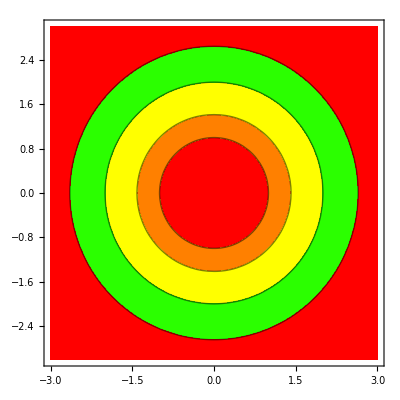

```mathematica
g[x_,y_]:=x^2+y^2

Plot3D[g[x,y],{x,-1,1},{y,-1,1}]
ContourPlot[g[x,y],{x,-3,3},{y,-3,3},Contours->{1,2,4,7},ColorFunction->Hue]
```

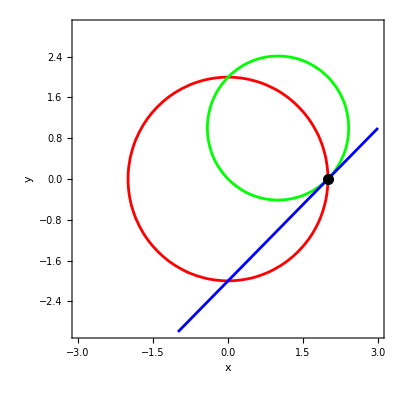

{{x→2,y→0}}

```mathematica
ContourPlot[{x^2+y^2==4,(x-1)^2+(y-1)^2==2,y==x-2},{x,-3,3},{y,-3,3},ContourStyle->{Red,Green,Blue},Axes->True,FrameLabel->{"x", "y"},Epilog->{PointSize[0.02],Point[{x,y}/.sol]}]
sol=Solve[{x^2+y^2==4 && (x-1)^2+(y-1)^2==2 && y==x-2},{x,y}]
```

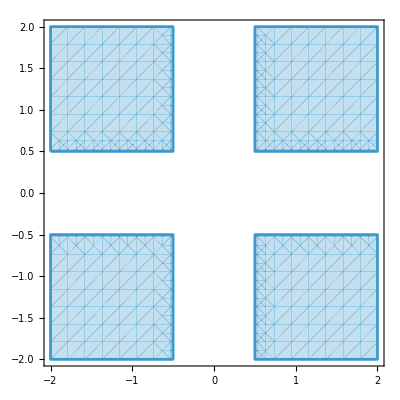

```mathematica
RegionPlot[x^2>0.25&&y^2>0.25,{x,-2,2},{y,-2,2}]
```

9.81

{1.,1.1/(1+0.1 Cos[p]),1.2/(1+0.2 Cos[p]),1.3/(1+0.3 Cos[p]),1.4/(1+0.4 Cos[p]),1.5/(1+0.5 Cos[p]),1.6/(1+0.6 Cos[p]),1.7/(1+0.7 Cos[p]),1.8/(1+0.8 Cos[p])}

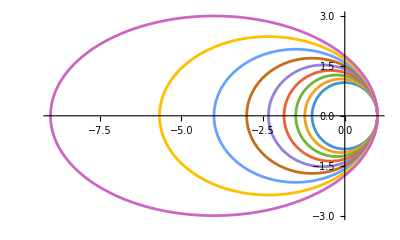

```mathematica
g=9.81
x[t_]:=v0 Cos[α] t
y[t_]:=v0 Sin[α]t - 0.5g t^2
Manipulate[ParametricPlot[{x[t],y[t]}/.{α->angle,v0->vel},{t,0,2(v0 Sin[α])/g/.{α->angle,v0->vel}},PlotRange->{{0,40},{0,20}}],{angle,0.0001,π/2},{vel,0.0001,20}]
r[p,q]:=(1+q)/(1+q Cos[p])
Table[r[p,q],{q,0,0.8,0.1}]
PolarPlot[Evaluate[Table[r[p,q],{q,0,0.8,0.1}]],{p,0,2π}]
```

# Macierze

```mathematica
A={{a11,a12},{a21,a22}};
B={{b11,b12},{b21,b22}};
{MatrixForm[A],MatrixForm[B]}
MatrixForm[A-B]
MatrixForm[Dot[A,B]]
MatrixForm[Inverse[B]]
```

{(a11 | a12
a21 | a22),(b11 | b12
b21 | b22)}

(a11-b11 | a12-b12
a21-b21 | a22-b22)

(a11 b11+a12 b21 | a11 b12+a12 b22
a21 b11+a22 b21 | a21 b12+a22 b22)

(b22/(-b12 b21+b11 b22) | -b12/(-b12 b21+b11 b22)
-b21/(-b12 b21+b11 b22) | b11/(-b12 b21+b11 b22))

```mathematica
S=A+B
MatrixForm[IdentityMatrix[S]]
MatrixForm[Inverse[S]]
```

{{a11+b11,a12+b12},{a21+b21,a22+b22}}

IdentityMatrix[{{a11+b11,a12+b12},{a21+b21,a22+b22}}]

```mathematica
({{(a22+b22)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22)), (-a12-b12)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22))}, {(-a21-b21)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22)), (a11+b11)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22))}})
```

{{(a22+b22)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22)),(-a12-b12)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22))},{(-a21-b21)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22)),(a11+b11)/(-((a12+b12) (a21+b21))+(a11+b11) (a22+b22))}}

# Dopasowanie krzywych

```mathematica
path= StringJoin[NotebookDirectory[],"neutrons.txt"]
data[= Import[path];
```

/dmj/2025/tb479789/TIK/wolfram/neutrons.txt

```mathematica
plot=ListPlot[data,PlotRange->{{0,45},{0,1.2}},PlotMarkers->"x",GridLines->Automatic,Frame->True,FrameLabel->{"N/N_0","t"}]
fit[]
```

ListPlot::lpn: data is not a list of numbers or pairs of numbers.

ListPlot[data,PlotRange→{{0,45},{0,1.2}},PlotMarkers→x,GridLines→Automatic,Frame→True,FrameLabel→{N/N_0,t}]

fit[]